```mathematica
Assuming[{m>0,Ω>0,X>0},A/π/Ω*Integrate[1/Sqrt[2X/(m Ω^2)-x^2],{x,-Sqrt[2*X/m/Ω^2],Sqrt[2*X/m/Ω^2]}]]
```

A/Ω

```mathematica
Assuming[{μ>0,u>1,u1≥0,x∈Reals},Integrate[x^(μ-1)/(1-x),{x,0,u}]]
```

Beta[1/u,1-μ,0]+π (-ⅈ+Cot[π μ])

```mathematica
Limit[Beta[1-x,μ,0]-Beta[1-x,1-μ,0],x->0]
```

PolyGamma[0,1-μ]-PolyGamma[0,μ]

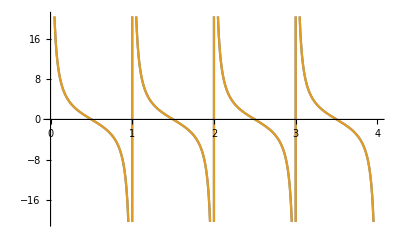

```mathematica
Plot[{PolyGamma[0,1-μ]-PolyGamma[0,μ],π*Cot[π*μ]},{μ,0,4}]
```

```mathematica
Beta[0,1-μ,0]
```

Beta[0,1-μ,0]

```mathematica
Manipulate[Plot[Limit[Beta[1-x,1+μ,0]-Beta[1/uc,1-x,-μ,0],x->0],{μ,0,4}],{u,10,100}]
```

```mathematica
Limit[Beta[1-x,1+μ,0]-Beta[1/uc,1-x,-μ,0],x->0]
```

Beta[1/uc,-μ,0]+PolyGamma[0,-μ]-PolyGamma[0,1+μ]

```mathematica
Manipulate[Plot[-x^μ*(Beta[1/uc,-μ,0]+PolyGamma[0,-μ]-PolyGamma[0,1+μ]),{x,0,20},PlotRange->{0,1000}],{uc,10,1000},{μ,0.001,4}]
```

```mathematica
FullSimplify[PolyGamma[0,-μ]-PolyGamma[0,1+μ]]
```

π Cot[π μ]

```mathematica
Manipulate[Plot[(Beta[1/u,1-μ,0]+π (Cot[π μ]))/u^(μ-1),{μ,0,4}],{u,10,1000000}]
```

```mathematica
Manipulate[Plot[Beta[1/u,1-μ,0],{μ,0,2}],{u,10,10000000}]
```

```mathematica
u*Integrate[x^(-μ)/(1-x),{x,0,1/u}]
```

ConditionalExpression[u Beta[1/u,1-μ,0],(Re[u]≥1||Re[u]≤0||u∉Reals)&&Re[μ]<1]

```mathematica
Limit[(Beta[1/u,1-μ,0]+π (Cot[π μ]))/u^(μ-1),u->∞]
```

```mathematica
Manipulate[Plot[{π*Cot[π*μ],Beta[1/u,1-μ,0]+π*Cot[π*μ]},{μ,0,4},PlotRange->{-100,100}],{u,1,10000000}]
```

```mathematica
Assuming[μ>0,Limit[(Beta[1/u,1-μ,0]+π (-ⅈ+Cot[π μ]))/u^(μ-1),u->∞]]
```

Limit[u^(1-μ) (Beta[1/u,1-μ,0]+π (-ⅈ+Cot[π μ])),u→∞]

```mathematica
Limit[Beta[1/u,1-μ,0]-Beta[1/u1,1-μ,0],u->∞]
```

```mathematica
Limit[Beta[0,1-μ,0]-Beta[1/u1,1-μ,0],u1->0]
```

Limit[Beta[0,1-μ,0]-Beta[1/u1,1-μ,0],u1→0]

```mathematica
Manipulate[Plot[Beta[1/u,1-μ,0]-Beta[1/u1,1-μ,0],{μ,0,4}],{u1,0,1},{u,1,1000}]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

```mathematica
Limit[Assuming[a>0,Integrate[z^(μ-1)/(z-a),{z,0,1}]],a->0]
```

ConditionalExpression[Undefined,Re[μ]>0]